```mathematica
f[x_]:=Abs@Log[10.,x];

res={0.9999987219762226,0.9999797155063298,0.9958434271664687,0.9407679303255253,0.7897684481557612,0.6305482172135245,0.5178623351411665,0.46782969523681833,0.44793637950571075,0.44008231127111674,0.43696980983186323};
massRange=Range[5,7,0.2];
gRange=Range[6,1,-1.];

massres=Transpose[{massRange,res}];

(*data=Flatten[Table[{i[[1]],j,i[[2]]},{i,massres},{j,gRange}],1];*)
data={{5.,6.,1.},{5.,5.,0.97},{5.,4.,0.97},{5.,3.,0.97},{5.,2.,0.97},{5.,1.,0.97},{5.4,6.,0.97},{5.4,5.,0.97},{5.4,4.,0.97},{5.4,3.,0.97},{5.4,2.,0.97},{5.4,1.,0.97},{5.6,6.,0.9400000000000001},{5.6,5.,0.9400000000000001},{5.6,4.,0.9500000000000001},{5.6,3.,0.96},{5.6,2.,0.97},{5.6,1.,0.97},{5.7,6.,0.88},{5.7,5.,0.88},{5.7,4.,0.89},{5.7,3.,0.92},{5.7,2.,0.96},{5.7,1.,0.97},{5.8,6.,0.79},{5.8,5.,0.79},{5.8,4.,0.8200000000000001},{5.8,3.,0.87},{5.8,2.,0.93},{5.8,1.,0.97},{5.9,6.,0.71},{5.9,5.,0.71},{5.9,4.,0.75},{5.9,3.,0.8200000000000001},{5.9,2.,0.9},{5.9,1.,0.97},{6.,6.,0.63},{6.,5.,0.64},{6.,4.,0.6900000000000001},{6.,3.,0.77},{6.,2.,0.88},{6.,1.,0.97},{6.1,6.,0.56},{6.1,5.,0.58},{6.1,4.,0.64},{6.1,3.,0.74},{6.1,2.,0.86},{6.1,1.,0.96},{6.2,6.,0.52},{6.2,5.,0.54},{6.2,4.,0.6},{6.2,3.,0.72},{6.2,2.,0.85},{6.2,1.,0.96},{6.4,6.,0.47000000000000003},{6.4,5.,0.49},{6.4,4.,0.5700000000000001},{6.4,3.,0.6900000000000001},{6.4,2.,0.84},{6.4,1.,0.9500000000000001},{6.6,6.,0.45},{6.6,5.,0.48},{6.6,4.,0.56},{6.6,3.,0.68},{6.6,2.,0.8300000000000001},{6.6,1.,0.9500000000000001},{6.8,6.,0.44},{6.8,5.,0.47000000000000003},{6.8,4.,0.55},{6.8,3.,0.68},{6.8,2.,0.8300000000000001},{6.8,1.,0.9500000000000001},{7.,6.,0.44},{7.,5.,0.47000000000000003},{7.,4.,0.55},{7.,3.,0.68},{7.,2.,0.8300000000000001},{7.,1.,0.9500000000000001},
{5.,0.,0.97},{5.,-1.,0.97},{5.4,0.,0.97},{5.4,-1.,0.97},{5.6,0.,0.97},{5.6,-1.,0.97},{5.7,0.,0.97},{5.7,-1.,0.97},{5.8,0.,0.97},{5.8,-1.,0.97},{5.9,0.,0.97},{5.9,-1.,0.97},{6.,0.,0.97},{6.,-1.,0.97},{6.1,0.,0.97},{6.1,-1.,0.97},{6.2,0.,0.97},{6.2,-1.,0.97},{6.4,0.,0.96},{6.4,-1.,0.97},{6.6,0.,0.96},{6.6,-1.,0.97},{6.8,0.,0.96},{6.8,-1.,0.97},{7.,0.,0.96},{7.,-1.,0.97},
{8.,0.,0.96},{8.,-1.,0.97},{8.,6.,0.43},{8.,5.,0.47000000000000003},{8.,4.,0.55},{8.,3.,0.68},{8.,2.,0.8300000000000001},{8.,1.,0.9500000000000001}};

p1=ListDensityPlot[data,Mesh->None,InterpolationOrder->5,PlotLegends->BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Times" ,GrayLevel[0],14,AbsoluteThickness[0.5]]], PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[0.5]],FrameLabel->{Style["m, eV",GrayLevel[0],16,AbsoluteThickness[0.5]],Style[Superscript["g, GeV" ,-1],GrayLevel[0],16,AbsoluteThickness[0.5]]}, GridLines->None,PlotRangePadding->0,PerformanceGoal->"Quality",
ColorFunction->(ColorData[{"Rainbow","Reverse"}][Rescale[#,{0.5,1.05}]]&),ColorFunctionScaling->False]

Export["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Charts\\Final\\3.svg",p1];
```

```mathematica
f[x_]:=Abs@Log[10.,x];
massSet={10^(-5),9*10^(-6),8*10^(-6),7*10^(-6),6*10^(-6),5*10^(-6),4*10^(-6),3*10^(-6),2*10^(-6),1*10^(-6),10^(-7),10^(-8)};
f@massSet
Log[10,9.*10^(-19)]
```

{5.,5.04576,5.09691,5.1549,5.22185,5.30103,5.39794,5.52288,5.69897,6.,7.,8.}

-18.0458

```mathematica
t=Import["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Mixing_data\\Radial_lambda_data.dat"];
ta=Table[
{i[[1]],i[[2]]*10-9,i[[3]]}
,
{i,t}]
```

```mathematica
{{8.,0.,0.96},{8.,-1.,0.97},{8.,-2.,0.98}}
```

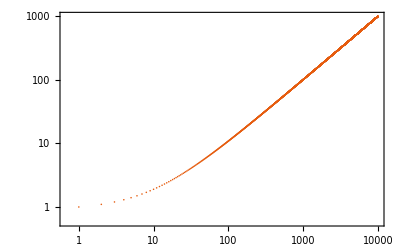

```mathematica
xRange=Range[1,1000,0.1];
yRange=Range[1,Length[xRange]];

ListLogLogPlot[Transpose[xRange,yRange],PlotLegends->BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Times" ,GrayLevel[0],14,AbsoluteThickness[0.5]]], PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[0.5]]]
```

```mathematica
10^(-5.8)
```

1.58489×10^-6